```mathematica
data={40, 33, 36, 35, 45, 33, 43, 39};
```

```mathematica
expandedData=Table[PadRight[{}, data[[i]],i], {i, 1, 8}]//Flatten
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8}

```mathematica
Mean[𝒰]//N
StandardDeviation[𝒰]//N
```

4.5

2.29129

```mathematica
Mean[expandedData]//N
StandardDeviation[expandedData]//N
```

4.57237

2.30969

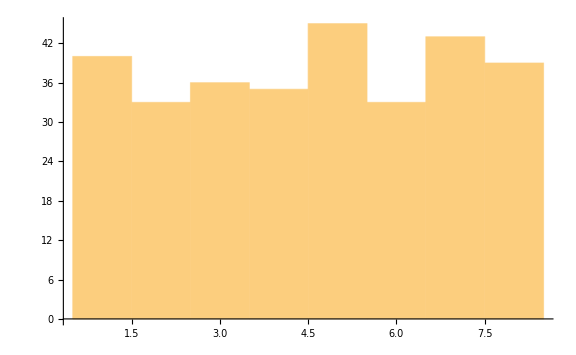

```mathematica
Histogram[expandedData, ImageSize->Large]
```

```mathematica
𝒰=FindDistribution[expandedData]
```

DiscreteUniformDistribution[{1,8}]

```mathematica
PearsonChiSquareTest[expandedData, 𝒰]
```

0.80954

```mathematica
DistributionFitTest[expandedData, 𝒰]
```

0.80954

```mathematica
DistributionFitTest[RandomSample[expandedData], 𝒰]
```

0.80954

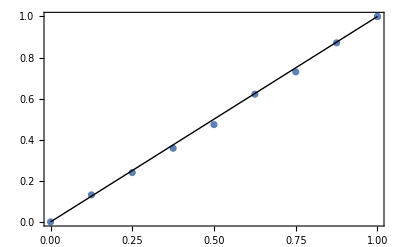

```mathematica
ProbabilityPlot[expandedData,𝒰]
```

```mathematica
DistributionFitTest[RandomSample[expandedData], 𝒰]
```

0.80954

```mathematica
DistributionFitTest[RandomVariate[𝒰, 10Length[expandedData]], 𝒰]
```

0.711827